```mathematica
data=Import["C:\\Users\\pizza\\iCloudDrive\\MSU\\CMSE 823\\Project\\CMSE823-Proj-BiCG\\project\\code\\task5.txt"];
```

```mathematica
splitData=StringSplit[data];
```

```mathematica
errors=Interpreter["Number"]/@Partition[splitData,2];
```

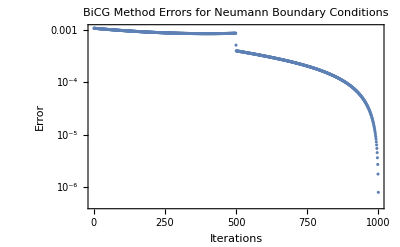

```mathematica
ListLogPlot[errors,Frame->True,FrameLabel->{"Iterations","Error"},PlotLabel->"BiCG Method Errors for Neumann Boundary Conditions"]
```